## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)

(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/freecad/";
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/freecad/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.0798942 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Feb 18, 2020, time: 12:46:19

nb: /Users/dantopa/Mathematica_files/nb/ert/freecad/mesh-sealer-ptw-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.0798942 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

#### functions

#### substitutions

#### modules

## 1 read data

```mathematica
data=Import[dirData<>"PTW.facet","Data"];
```

```mathematica
Dimensions[data]
```

{1039}

```mathematica
data[[20]]
```

{15000.000000  3013.514893  -457.200012}

```mathematica
First[StringSplit[data[[20]]]]
%[[1]]
```

{15000.000000,3013.514893,-457.200012}

15000.000000

```mathematica
data[[5]][[1]]
```

345

## 2 gather points

```mathematica
nPoints=data[[5]][[1]]
p=Table[
Read[StringToStream[#],Number]&/@First[StringSplit[data[[k]]]]
,{k,6,5+nPoints}];
```

345

```mathematica
p[[3]]
```

{3658.,-10450.,457.2}

## 3 radial sort

```mathematica
list={Range[nPoints],p}ᵀ;
```

```mathematica
radialList={#[[1]],Norm[#[[2]],2]}&/@list;
```

```mathematica
sortedRadialList=Sort[radialList,#1[[2]]<#2[[2]]&];
```

```mathematica
sortedRadialList[[300;;345]]
```

{{170,34239.7},{155,34239.7},{167,34239.7},{158,34239.7},{171,34239.7},{154,34239.7},{50,35730.2},{131,36456.3},{127,36456.3},{166,36456.3},{153,36456.3},{130,36456.3},{128,36456.3},{174,36456.3},{164,38674.},{152,38674.},{165,38674.},{151,38674.},{177,38674.},{175,38674.},{173,38674.},{160,38674.},{51,40165.8},{163,40892.4},{150,40892.4},{126,40892.4},{125,40892.4},{178,40892.4},{176,40892.4},{133,40892.4},{180,43111.5},{179,43111.5},{161,43111.5},{149,43111.5},{182,43111.5},{181,43111.5},{162,43111.5},{148,43111.5},{261,44525.2},{262,44532.},{263,44551.9},{41,44604.3},{40,44604.3},{9,44604.3},{42,44604.3},{39,44604.3}}

## process

```mathematica
counter=0;
duplicates={};
deltaNorm={};
Clear[checker];
checker[k_Integer]:=Module[{},
(* radii of points being compared *)
A=sortedRadialList[[k]][[2]];
B=sortedRadialList[[k+1]][[2]];
(* indices of points being compared *)
indexA=sortedRadialList[[k]][[1]];
indexB=sortedRadialList[[k+1]][[1]];
(* points being compared *)
pA=p[[indexA]];
pB=p[[indexB]];
(* norm of difference of points *)
ζ=Norm[pA-pB,2];
If[ζ<0.01,Print["* * * Duplicate "<>lf],Return[]];
(* duplicate found *)
counter+=1;
AppendTo[duplicates,{indexA,indexB}];
AppendTo[deltaNorm,ζ];
Print["k = ",k];
Print["radius difference = ",Abs[A-B]];
Print["index(A) = ",indexA];
Print["index(B) = ",indexB];
Print["p(A) = ",pA];
Print["p(B) = ",pB];
Print["norm(pA-pB) = ",ζ];
]
```

```mathematica
Δ=0.01;
Do[
(* compare radii *)
A=sortedRadialList[[k]][[2]];
B=sortedRadialList[[k+1]][[2]];
If[Abs[A-B]<Δ,checker[k]]
,{k,nPoints-1}]
```

```mathematica
counter
duplicates
```

```mathematica
A
```

44604.3

## how close?

```mathematica
indx=sortedRadialList[[All,1]]
Length[%]
```

{58,57,259,260,14,11,8,5,52,10,139,135,138,136,197,112,107,101,194,188,195,187,200,198,196,189,13,12,7,6,43,106,338,193,186,115,114,201,199,140,109,103,62,59,38,35,264,110,104,61,60,37,36,209,202,191,185,218,217,192,184,111,105,108,102,44,339,137,134,210,203,142,141,216,265,341,100,26,23,4,2,340,99,25,24,3,1,212,206,214,204,211,207,190,183,45,215,205,124,121,213,208,118,21,19,16,15,268,93,84,67,63,311,317,288,254,250,255,249,253,251,231,219,326,297,46,92,83,68,64,325,296,279,272,266,122,120,123,119,256,56,55,54,53,327,298,276,269,333,304,321,292,315,286,309,91,82,69,65,323,294,252,248,232,221,258,257,233,220,316,287,335,306,280,273,334,305,337,308,278,271,324,295,47,22,20,18,17,281,274,330,301,285,90,81,70,66,267,234,222,117,116,247,245,147,97,88,77,72,314,322,293,336,307,96,87,78,73,320,291,283,329,300,310,235,224,236,223,246,244,242,230,33,31,28,27,282,275,319,290,312,95,86,79,74,345,343,332,303,277,270,48,331,302,328,299,146,143,237,225,145,144,243,98,89,76,71,94,85,80,75,284,344,342,318,289,239,228,240,227,238,229,241,226,313,34,32,30,29,49,172,156,132,129,169,159,113,168,157,170,155,167,158,171,154,50,131,127,166,153,130,128,174,164,152,165,151,177,175,173,160,51,163,150,126,125,178,176,133,180,179,161,149,182,181,162,148,261,262,263,41,40,9,42,39}

345

```mathematica
diffs=Table[
ia=indx[[k]];
ib=indx[[k+1]];
A=p[[ia]];
B=p[[ib]];
Norm[A-B,2]
,{k,nPoints-1}]
```

{914.4,1324.68,3285.88,5076.74,914.4,6027.03,914.4,4622.52,6096.,1957.03,3467.2,6051.97,4561.77,2501.09,5230.87,1925.98,914.4,6933.3,5819.2,6051.97,5219.08,4561.77,2501.09,5819.2,1104.8,4434.44,914.4,6027.03,914.4,4052.26,5239.98,10739.8,7109.72,3467.2,2501.09,6051.97,5819.2,4561.77,2501.09,8421.51,914.4,13118.7,914.4,13463.5,914.4,13167.9,12305.3,914.4,13118.7,914.4,13463.5,914.4,5523.28,5819.2,2501.09,5219.08,5819.2,2501.09,6051.97,1104.8,11021.9,3658.,2057.64,914.4,11712.9,13420.9,12666.7,3467.2,2501.09,6051.97,5819.2,4561.77,2501.09,11686.1,3386.06,20900.,20908.6,914.4,20900.,914.4,21128.,20900.,20913.5,914.4,20900.,914.4,11220.4,5819.2,6051.97,5219.08,5819.2,2501.09,5819.2,1104.8,1595.43,1956.94,3467.2,5219.08,6051.97,5819.2,4561.77,2501.09,4079.41,914.4,6096.,914.4,1893.71,11451.1,914.4,13181.6,914.4,13288.4,3705.69,914.4,6274.49,5819.2,6051.97,5219.08,5819.2,2501.09,5819.2,1104.8,8736.2,914.4,8067.73,11113.8,914.4,20336.2,914.4,15699.5,914.4,13510.,914.4,3535.34,13681.8,3467.2,6051.97,4561.77,2501.09,3976.2,914.4,6096.,914.4,6293.97,914.4,7753.53,914.4,14168.5,914.4,2622.55,914.4,5000.27,914.4,7066.51,519.02,914.4,27490.8,914.4,19703.4,914.4,8408.94,5819.2,2501.09,5219.08,5819.2,2501.09,6051.97,1104.8,5123.43,914.4,8909.4,914.4,23478.4,914.4,21386.9,914.4,5000.26,914.4,22234.4,914.4,15611.1,914.4,7988.39,4622.99,914.4,6096.,914.4,13646.3,914.4,31356.7,914.4,21720.7,23354.1,914.4,34645.4,914.4,556.276,21101.4,3467.2,2501.09,6051.97,5819.2,4561.77,2501.09,7112.7,914.4,13213.3,914.4,13288.4,5199.68,914.4,2622.55,914.4,4510.46,914.4,20356.8,914.4,26424.2,914.4,27479.5,29767.2,914.4,3305.88,20191.8,5819.2,6051.97,5219.08,4561.77,2501.09,5819.2,1104.8,24005.4,914.4,41800.,914.4,7987.64,914.4,35899.8,914.4,9115.15,519.02,914.4,27506.,914.4,35191.5,41800.,37220.3,914.4,35062.7,914.4,20774.5,19668.1,914.4,2622.55,914.4,20584.7,3467.2,5219.08,6051.97,5819.2,4561.77,2501.09,22813.4,914.4,41810.,914.4,38408.2,914.4,34657.5,914.4,556.276,38605.7,41800.,41159.2,914.4,19370.2,5819.2,6051.97,5219.08,5819.2,2501.09,6051.97,1104.8,22317.2,746.616,914.4,41810.,914.4,22837.7,1956.83,3467.2,5219.08,6051.97,5819.2,4561.77,2501.09,4242.14,5819.2,6051.97,5219.08,5819.2,2501.09,6051.97,1104.8,1595.77,1956.81,3467.2,5219.08,6051.97,5819.2,4561.77,2501.09,4242.13,5819.2,6051.97,5219.08,4561.77,2501.09,5819.2,1104.8,1595.84,1956.78,3467.2,5219.08,6051.97,2501.09,4561.77,2501.09,4242.13,5819.2,2501.09,5219.08,5819.2,2501.09,6051.97,1104.8,3225.79,3036.46,3036.46,5195.02,3583.14,5797.64,3583.14,5797.64}

## visuals

```mathematica
radii=Norm[#[[2]],2]&/@list;
```

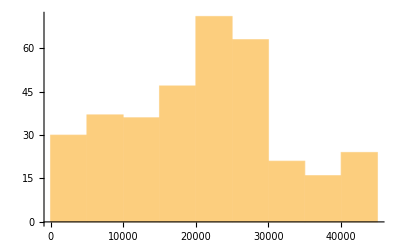

```mathematica
Histogram[radii]
```

```mathematica
ListPointPlot3D[p]
```

-Graphics3D-

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```